```mathematica
FullSimplify[ComplexExpand[Re[Exp[-I psi]Zr Exp[I th]]/Cos[psi]]]
```

Zr (Cos[th]+Sin[th] Tan[psi])

```mathematica
ds[{e_,m_},{ep_,mp_}]:=e mp-m ep;
```

```mathematica
mon[{e_,m_}]:={{1-e m,e^2},{-m^2,1+e m}};
```

```mathematica
dsDim[{n1_,n2_,n3_},{n1p_,n2p_,n3p_}]:={n1,n2,n3}.matMassive.{n1p,n2p,n3p};
```

```mathematica
(* going around a massless object {e, m} *)
{ep,mp}-ds[{e,m},{ep,mp}]{e,m}
Simplify[%.(mon[{e,m}]ᵀ.{a,aD})-{ep,mp}.{a,aD}]
```

{ep-e (-ep m+e mp),mp-m (-ep m+e mp)}

0

```mathematica
ClearAll[QuiverPlot];
QuiverPlot[dsz_?MatrixQ]:=Module[{n=Length[dsz],edges},edges=Flatten@Table[Which[dsz[[i,j]]>0,ConstantArray[DirectedEdge[i,j],dsz[[i,j]]],dsz[[i,j]]<0,ConstantArray[DirectedEdge[j,i],-dsz[[i,j]]],True,{}],{i,n},{j,i+1,n}];
Graph[Range[n],edges,VertexLabels->"Name",GraphLayout->"CircularEmbedding",EdgeLabels->(e_:>Length@Cases[edges,e]),EdgeStyle->Arrowheads[0.1],VertexSize->Small,ImageSize->Small]]
```

```mathematica
Massive={{0,1},{2,-1},{-1,0}};
```

```mathematica
Total[Massive]
```

{1,0}

```mathematica
{Massive[[1]], Massive[[2]]+Massive[[3]],-Massive[[3]]}
```

{{0,1},{1,-1},{1,0}}

```mathematica
Massless={{0,1},{1,-1},{1,0}};
```

```mathematica
Total[Massless]
```

{2,0}

{{0,-2,1},{2,0,-1},{-1,1,0}}

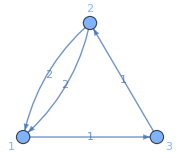

```mathematica
matMassive=Outer[ds,Massive,Massive,1]
QuiverPlot[%]
```

{{0,-1,-1},{1,0,1},{1,-1,0}}

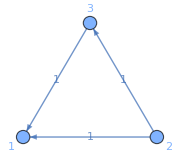

```mathematica
matMassless=Outer[ds,Massless,Massless,1]
QuiverPlot[%]
```

```mathematica
zet={-u+v Sqrt[3]+1/3,2u+1/3,-u-v Sqrt[3]+1/3};
```

```mathematica
Total[zet]
```

1

```mathematica
Collect[n1 zet[[1]]+n2 zet[[2]]+n3 zet[[3]],{n1,n2,n3}]
Simplify[D[%,{{u,v}}]]
Simplify[-{%[[2]],-%[[1]]}]
```

n2 (1/3+2 u)+n3 (1/3-u-√3 v)+n1 (1/3-u+√3 v)

{-n1+2 n2-n3,√3 (n1-n3)}

{√3 (-n1+n3),-n1+2 n2-n3}

```mathematica
FullSimplify[{u,v}/.First[Solve[{n1 zet[[1]]+n2 zet[[2]]+n3 zet[[3]]==0,nn1 zet[[1]]+nn2 zet[[2]]+nn3 zet[[3]]==0}, {u,v}]]]
```

{(n3 (2 nn1+nn2)+n2 (nn1-nn3)-n1 (nn2+2 nn3))/(6 (n3 (nn1-nn2)+n1 (nn2-nn3)+n2 (-nn1+nn3))),((n1+n3) nn2-n2 (nn1+nn3))/(2 √3 (n3 (-nn1+nn2)+n2 (nn1-nn3)+n1 (-nn2+nn3)))}

```mathematica
Simplify[ds[{n1,n2,n3}.Massive,{nn1,nn2,nn3}.Massive]]
Simplify[%/(6 (n3 (nn1-nn2)+n1 (nn2-nn3)+n2 (-nn1+nn3)))]
```

2 n2 nn1-n3 nn1-2 n1 nn2+n3 nn2+n1 nn3-n2 nn3

(n3 nn1+2 n1 nn2-n3 nn2-n1 nn3+n2 (-2 nn1+nn3))/(6 (n3 (-nn1+nn2)+n2 (nn1-nn3)+n1 (-nn2+nn3)))

```mathematica
inter[{n1_,n2_,n3_},{nn1_,nn2_,nn3_}]:={(n3 (2 nn1+nn2)+n2 (nn1-nn3)-n1 (nn2+2 nn3))/(6 (n3 (nn1-nn2)+n1 (nn2-nn3)+n2 (-nn1+nn3))),((n1+n3) nn2-n2 (nn1+nn3))/(2 √3 (n3 (-nn1+nn2)+n2 (nn1-nn3)+n1 (-nn2+nn3)))};
```

```mathematica
vec[{n1_,n2_,n3_}]:={√3 (-n1+n3),-n1+2 n2-n3};
```

```mathematica
rayeq[{n1_,n2_,n3_}]:=n2 (1/3+2 u)+n3 (1/3-u-√3 v)+n1 (1/3-u+√3 v);
```

```mathematica
inter[{1,0,0},{0,1,0}]
```

{-1/6,-1/(2 √3)}

```mathematica
inter[{0,1,0},{0,0,1}]
```

{-1/6,1/(2 √3)}

```mathematica
inter[{0,0,1},{1,0,0}]
```

{1/3,0}

```mathematica
vec[{0,0,1}]
```

{√3,-1}

```mathematica
ClearAll[plotLine];
plotLine[expr_,xr:{x_,_,_},yr:{y_,_,_}]:=ContourPlot[Evaluate[expr==0],xr,yr,ContourStyle->Thick]
```

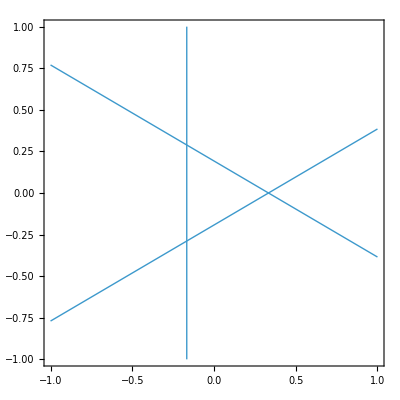

```mathematica
Show[
plotLine[rayeq[{1,0,0}],{u,-1,1},{v,-1,1}],
plotLine[rayeq[{0,1,0}],{u,-1,1},{v,-1,1}],
plotLine[rayeq[{0,0,1}],{u,-1,1},{v,-1,1}]
]
```

```mathematica
{{0,1},{-1,1},{-2,1}}
MatrixForm@Outer[ds,%,%,1]
```

{{0,1},{-1,1},{-2,1}}

(0 | 1 | 2
-1 | 0 | 1
-2 | -1 | 0)

```mathematica
{{0,1},{-1,1},{1,1}}
MatrixForm@Outer[ds,%,%,1]
```

{{0,1},{-1,1},{1,1}}

(0 | 1 | -1
-1 | 0 | -2
1 | 2 | 0)

```mathematica
zet
```

{1/3-u+√3 v,1/3+2 u,1/3-u-√3 v}

```mathematica
-{n3-2n2,2n1-n3,n2-n1}
%.
```

{2 n2-n3,-2 n1+n3,n1-n2}

## package testing

```mathematica
1+1
```

2

```mathematica
<<MaTeX`;
```

```mathematica
Quiet[Remove["SWNf1QuiverScattering`*","SWNf1QuiverScattering`Private`*"]];
<<"/Users/rishi/Developer/localf1/notebooks/sw_nf1/SWNf1QuiverScattering.m"
```

SWNf1QuiverScattering 1.0, June 2025 - Generic quiver scattering diagram machinery

```mathematica
Mat
```

{{0,-2,1},{2,0,-1},{-1,1,0}}

```mathematica
?ConstructMcKayDiagram
```

```mathematica
ListRays=ConstructMcKayDiagram[100000,10,0,{}];
```

Adding 11 rays,

Adding 4 rays,

18 in total.

Part::partd: Part specification SWNf1QuiverScattering`Private`Nvec⟦1⟧ is longer than depth of object.

Part::partd: Part specification SWNf1QuiverScattering`Private`Nvec⟦2⟧ is longer than depth of object.

Part::partd: Part specification SWNf1QuiverScattering`Private`Nvec⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

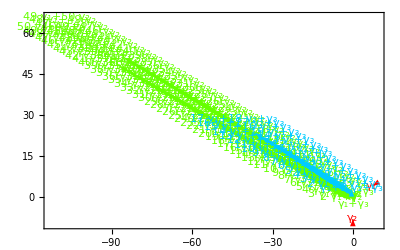

```mathematica
Graphics[Table[{Hue[0.8 (ListRays[[k,7]]-1)/Max[ListRays[[All,7]]]],Arrow[{ListRays[[k,2]],ListRays[[k,2]]+McKayVec[ListRays[[k,1]]]/Max[1,GCD@@ListRays[[k,1]]]}],Text[ListRays[[k,1]]/. McKayrep,ListRays[[k,2]]+1.3 McKayVec[ListRays[[k,1]]]/Max[1,GCD@@ListRays[[k,1]]]]},{k,Length[ListRays]}],Frame->True]
```

```mathematica
Massive
```

{{0,1},{2,-1},{-1,0}}

```mathematica
ds[{2,3,1}.Massive,{1,2,0}.Massive]
```

-1

```mathematica
McKayIntersectRays[{2,3,1},{1,2,0},0]
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,ComplexInfinity}

```mathematica
{1,0,0}/.McKayrep
```

γ_1

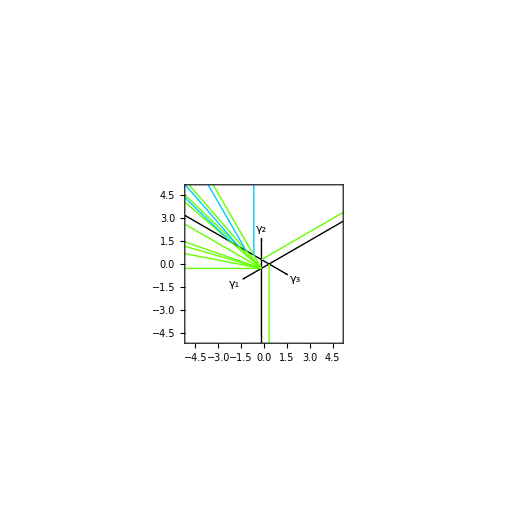

```mathematica
Module[{L=6,sc=5},Graphics[Table[{If[ListRays[[k,3]]==0,{Thick,Red},Hue[0.8 (ListRays[[k,7]]-1)/Max[ListRays[[All,7]]]]],Arrow[{ListRays[[k,2]],ListRays[[k,2]]+L McKayVec[ListRays[[k,1]]]/Max[1,GCD@@ListRays[[k,1]]]}],Text[ListRays[[k,1]]/. McKayrep,ListRays[[k,2]]+(L+0.3) McKayVec[ListRays[[k,1]]]/Max[1,GCD@@ListRays[[k,1]]]]},{k,Length[ListRays]}],Frame->True, PlotRange->{{-sc,sc},{-sc,sc}}]]
```

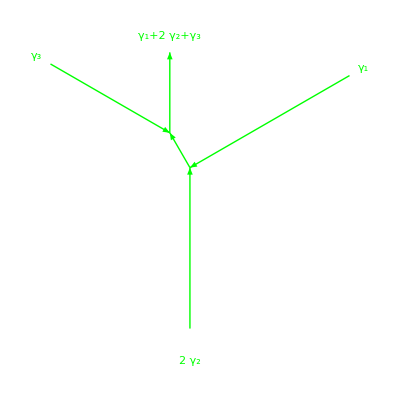

```mathematica
trees=McKayTreesFromListRays[ListRays,{1,2,1},0];
McKayScattDiag[trees,0]
```

```mathematica
MaTeX
```

Adding 5 rays,

8 in total.

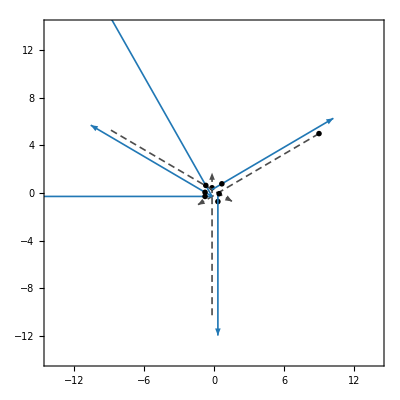

```mathematica
ListRays=ConstructMcKayDiagram[3,3,0,{}];
With[{sc=14},Show[McKayPlotDiagram[ListRays,0], PlotRange->{{-sc,sc},{-sc,sc}}]]
```

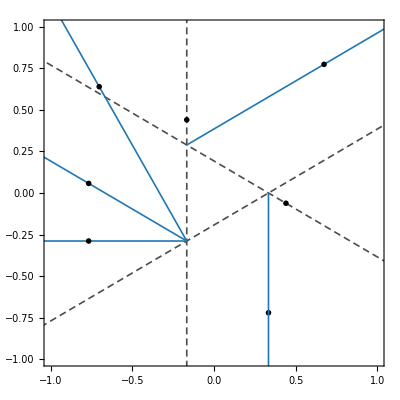

```mathematica
McKayPlotDiagram[ListRays,0]
```

## mutation classes

```mathematica
ClearAll[mutateB,mutationClass,arrows];

mutateB[B_,k_Integer]:=Module[{n=Length[B]},Table[If[i==k||j==k,-B[[i,j]],B[[i,j]]+Max[B[[i,k]],0] Max[B[[k,j]],0]-Max[-B[[i,k]],0] Max[-B[[k,j]],0]],{i,n},{j,n}]];

mutationClass[B0_]:=FixedPoint[DeleteDuplicates@Join[#,Flatten[Table[mutateB[B,k],{B,#},{k,Length[B0]}],1]]&,{B0}];

arrows[B_]:=Module[{n=Length[B]},Cases[Flatten[Table[Which[B[[i,j]]>0,{{i,j,B[[i,j]]}},B[[i,j]]<0,{{j,i,-B[[i,j]]}},True,{}],{i,n},{j,i+1,n}],2],{_Integer,_Integer,_Integer}]];

B0={{0,-2,1},{2,0,-1},{-1,1,0}};

cls=mutationClass[B0];

Length[cls]
arrows/@cls
```

12

{{{2,1,2},{1,3,1},{3,2,1}},{{1,2,2},{3,1,1},{2,3,1}},{{2,1,1},{3,1,1},{2,3,1}},{{1,2,1},{1,3,1},{3,2,1}},{{1,2,1},{1,3,1},{2,3,1}},{{1,2,1},{3,1,1},{3,2,1}},{{2,1,1},{3,1,1},{3,2,1}},{{2,1,1},{1,3,1},{2,3,1}},{{2,1,1},{1,3,2},{3,2,1}},{{2,1,1},{1,3,1},{3,2,2}},{{1,2,1},{3,1,2},{2,3,1}},{{1,2,1},{3,1,1},{2,3,2}}}